5

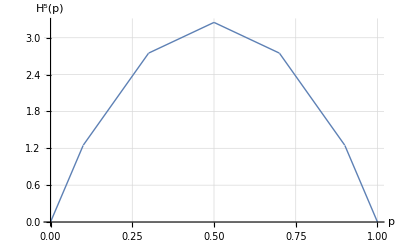

value_combination.eps

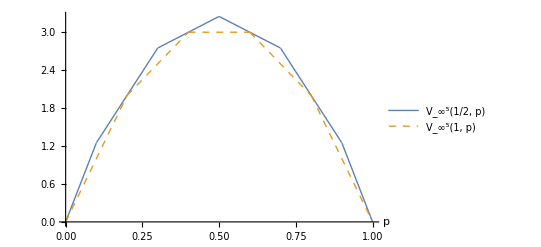

value_comparison.eps

```mathematica
omega[m_,k_,p_,beta_]:=1/2*(p*(m-k)*(m-k+1-2*beta) + (1-p)*k*(k+1-2*(1-beta)))
h[m_,p_,beta_]:=Min@@(omega[m,#,p,beta]&/@Range[0,m])
hDomansky[m_,p_]:=h[m,p,1]
hComb[m_,p_]:=h[m,p,1/2]
m=5
pCombination = Plot[
hComb[m,p],{p,0,1},
AxesLabel->{"p","H^5(p)"},
AxesStyle->Arrowheads[0.02],
PlotStyle->AbsoluteThickness[1],GridLines->Automatic
]
Export["value_combination.eps", pCombination]
pComparison = Plot[
{
hComb[m,p],
hDomansky[m,p]
},
{p,0,1},
PlotLegends->{"V_∞^5(1/2, p)","V_∞^5(1, p)"},AxesLabel->{"p",""},
AxesStyle->Arrowheads[0.02],
PlotStyle->{
{AbsoluteThickness[1]},
{AbsoluteThickness[1],Dashed}
}
]
Export["value_comparison.eps", pComparison]
```